## Plotting styles

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
Needs["MaTeX`"]//Quiet

FONTSIZE=25;
TEXSTYLE={FontFamily->"Latin Modern Roman",FontSize->FONTSIZE,FrameStyle->BlackFrame};

SetOptions[MaTeX,FontSize->FONTSIZE];

SetOptions[Plot,
PlotStyle->Thick,Axes->False,Frame->True,BaseStyle->TEXSTYLE];

Clear[FONTSIZE,TEXSTYLE,IMAGESIZE]
```

## Common functions

```mathematica
(*Function to calculate a list of beta function values Subscript[β, X](X)=dlnX/dlnN for a list of X values*)
B[{n_,X_}]:=Transpose@{Exp[(Log[X]⟦2;;⟧+Log[X]⟦;;-2⟧)/2],(Log[X]⟦2;;⟧-Log[X]⟦;;-2⟧)/(Log[n]⟦2;;⟧-Log[n]⟦;;-2⟧)};

(*The exact analytical participation entropy of an ΝxΝ GOE matrix, Ν>=2; it equals HarmonicNumber[Ν/2]-HarmonicNumber[1/2]*)
HaarS[Ν_]:=Ν Expectation[-x Log[x],x\[Distributed] BetaDistribution[1/2,(Ν-1)/2]]//Evaluate;
```

## Resonance counting for the Gaussian RP model

### Definitions

```mathematica
(*It may take a few minutes to evaluate*)
$Assumptions=Ω>1&&n>0&&γ>0&&0<w&&0<c<1;
pdf2[ξ_]:=Evaluate@PDF[TransformedDistribution[v^2,v\[Distributed]NormalDistribution[0,n^(-γ/2)]],ξ];
P[Ω_,c_]:=1-Integrate[2ξ(1-ξ/w) pdf2[ξ^2 c/Ω]c/Ω,{ξ,0,w}]//FullSimplify//Expand//Evaluate;
ψ2tails[Ω_,c_]:=Integrate[w^-1(√(ξ c/Ω)-ξ/w)pdf2[ξ],{ξ,0,w^2 c/Ω},Assumptions->c>0&&w>0&&Ω>1]//FullSimplify//Expand//Evaluate;
Integrate[w^-1(ξ/ω^2)Log[ξ/ω^2],{ω,√(ξ Ω/c),w},Assumptions->$Assumptions&&0<ξ<w^2 c/Ω];
Stails[Ω_,c_]:=-(n+1-Ω)Integrate[%pdf2[ξ],{ξ,0,c w^2/Ω},Assumptions->$Assumptions&&0<ξ<w^2 c/Ω]//FullSimplify//Expand//Evaluate;
```

### Numerical solution of the self - consistent resonance counting equations

```mathematica
w=1;γRange=Range[0.5,2.5,0.1];nRange=2^Range[4,300,0.25];

(*A lot of errors occur because the computational precision is not enough for large n. We filter unreliable results later*)
Off[FindRoot::lstol,FindRoot::cvmit,Power::infy,FindRoot::nlnum,Infinity::indet,General::ovfl]//ParallelEvaluate;
Sdata=ParallelTable[
{n,c HaarS[Ω]-c Log[c]+Stails[Ω,c],c}/.FindRoot[{c==1-(n+1-Ω)ψ2tails[Ω,c],Ω==1+n P[Ω,c]},{{Ω,n},{c,1}}],{γ,γRange},{n,nRange}]//Quiet;
Ddata={#[[1]],#[[2]]/Log@#[[1]]}&/@#&/@Sdata[[All,All,;;2]];
Clear[w]
```

### Plotting of the results

```mathematica
style=Table[Hue[0.75 (i-1)/Length@γRange],{i,Length@γRange}];

(*Participation entropy*)
Legended[#,Placed[#,{0.35,0.83}]&@Framed[#,RoundingRadius->5,FrameStyle->Gray,Background->Directive[Opacity[.5],White]]&@LineLegend[style,Table[MaTeX["\\gamma="<>ToString@DecimalForm[γ,{Infinity,1}]],{γ,γRange[[;;-2]]}],Spacings->0.1,LegendLayout->{"Column",6}]]&@ListPlot[Sdata[[;;-2,;;25,{1,2}]],
ScalingFunctions->{"Log2",None},PlotTheme->"Scientific",Joined->True,PlotStyle->Table[Hue[0.75(i-1)/Length@γRange,0.5],{i,Length@γRange}],FrameLabel->{MaTeX@"N",MaTeX@"S(N)"},ImageSize->800,PlotRange->{0.5,6.25},FrameTicks->{{Table[{x,MaTeX@DecimalForm[x,{Infinity,1}]},{x,0,6,1}],None},{Table[{2^x,MaTeX["2^{"<>ToString[x]<>"}"]},{x,4,10}],None}}]

(*Total head's weight*)
Legended[#,Placed[#,{0.73,0.515}]&@Framed[#,RoundingRadius->5,FrameStyle->Gray,Background->Directive[Opacity[.5],White]]&@LineLegend[style,Table[MaTeX["\\gamma="<>ToString@DecimalForm[γ,{Infinity,1}]],{γ,γRange[[;;-2]]}],Spacings->0.1,LegendLayout->{"Column",6}]]&@ListPlot[
Sdata[[;;-2,;;384,{1,3}]],
ScalingFunctions->{"Log2",None},PlotTheme->"Scientific",Joined->True,PlotStyle->style,FrameLabel->{MaTeX@"N",MaTeX@"C(N)"}, AspectRatio->1/3,ImageSize->1100,PlotRange->{{2^3,2^101},{0.45,1.05}},FrameTicks->{{Table[{x,MaTeX@DecimalForm[x,{Infinity,1}]},{x,0.5,1,0.1}],None},{Table[{2^x,MaTeX["2^{"<>ToString[x]<>"}"]},{x,4,100,16}],None}},GridLines->{None,{0.5,1}}]

(*Beta function of the support set dimension. We regularize Ddata by removing unreliable results lying beyond the Mathematica's numerical precision*)
regDdata=Join[{Ddata[[1,;;600]]},{Ddata[[2,;;650]]},{Ddata[[3,;;1050]]},Ddata[[4;;9]],{Ddata[[10,;;1007]]},{Ddata[[11,;;803]]},{Ddata[[12,;;667]]},{Ddata[[13,;;571]]},{Ddata[[14,;;499]]},{Ddata[[15,;;439]]},{Ddata[[16,;;395]]},{Ddata[[17,;;359]]},{Ddata[[18,;;327]]},{Ddata[[19,;;299]]},{Ddata[[20,;;281]]},{Ddata[[21,;;261]]}];
Legended[#,Placed[#,{0.305,0.82}]&@Framed[#,RoundingRadius->5,FrameStyle->Gray,Background->Directive[Opacity[.5],White]]&@LineLegend[style,Table[MaTeX["\\gamma="<>ToString@DecimalForm[γ,{Infinity,1}]],{γ,γRange[[;;16]]}],Spacings->0.1,LegendLayout->{"Column",5}]]&@ListPlot[B[#ᵀ]&/@regDdata[[;;16]],
PlotTheme->"Scientific",Joined->True,PlotStyle->style,FrameLabel->{MaTeX@"D",MaTeX@"\\beta(D)"},ImageSize->800,PlotRange->All,FrameTicks->{{Table[{x,MaTeX@DecimalForm[x,{Infinity,1}]},{x,-0.15,0.1,0.05}],None},{Table[{x,MaTeX@DecimalForm[x,{Infinity,1}]},{x,0,1,0.1}],None}}, GridLines->{Automatic,{0}}]
```

-Graphics-

-Graphics-

-Graphics-

## Comparison with PhysRevE.98.032139

### The model

```mathematica
ldos=ν->c/(ϵ^2+Γ^2); (*the Breit-Wigner formula with the spreading width Γ calculated by the Fermi golden rule*)
broadening=Γ->π n^(1-γ)/(2w);(*the spreading width Γ calculated by the Fermi golden rule*)
fluct=NormalDistribution[0,ν^(1/2)];(*the local Porter-Thomas law describing eigenstates components fluctuations*)
onsite=UniformDistribution[{-w,w}];(*the box distribution for the onsite energies*)
$Assumptions=Γ>0&&w>0&&ν>0&&n>1&&1<γ<2;
```

### Normalization

```mathematica
Expectation[ν/.ldos,ϵ\[Distributed]onsite]
norm=First@Flatten@Solve[%==1/n,c]
```

(c ArcTan[w/Γ])/(w Γ)

c→(w Γ)/(n ArcTan[w/Γ])

### Participation entropy & support set dimension

```mathematica
Expectation[-x^2 Log[x^2],x\[Distributed]fluct]
Expectation[%/.ldos,ϵ\[Distributed]onsite]
FullSimplify[n%/.norm](*Patricipation entropy; despite the expression contains imaginary unit, the result is real*)
d1[n_,γ_,w_]:=%/Log[n]/.broadening//Evaluate;
```

ν (-2+EulerGamma+Log[2]-Log[ν])

(c (ⅈ π^2-24 ArcTan[w/Γ]+12 EulerGamma ArcTan[w/Γ]+12 ⅈ ArcTan[w/Γ]^2+12 ArcTan[w/Γ] Log[2]+24 ArcTan[w/Γ] Log[-(2 ⅈ Γ)/(w-ⅈ Γ)]-12 ArcTan[w/Γ] Log[c/(w^2+Γ^2)]+12 ⅈ PolyLog[2,-1+(2 w)/(w-ⅈ Γ)]))/(12 w Γ)

-2+EulerGamma+(ⅈ π^2)/(12 ArcTan[w/Γ])+ⅈ ArcTan[w/Γ]+2 Log[-(2 ⅈ Γ)/(w-ⅈ Γ)]+Log[(2 n (w^2+Γ^2) ArcTan[w/Γ])/(w Γ)]+(ⅈ PolyLog[2,-1+(2 w)/(w-ⅈ Γ)])/ArcTan[w/Γ]

### Beta function of the support set dimension

```mathematica
Off[General::munfl]//ParallelEvaluate;
{t,bogData}=AbsoluteTiming@ParallelTable[{d1[n,γ,1],(n/d1[n,γ,1])Evaluate@D[d1[n,γ,1],n]}/.n->2^p,{γ,1,2,0.1},{p,4,1000,0.25}];t
```

19.9308

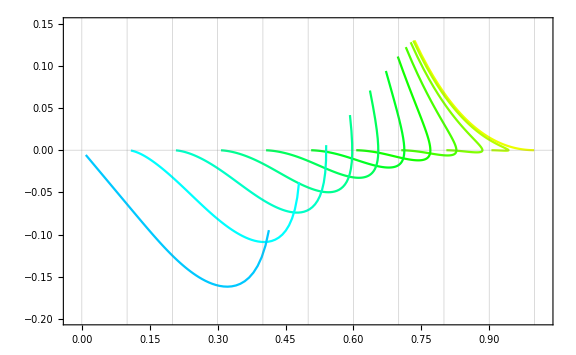

```mathematica
(*Below, we regularize bogData by removing unreliable results lying beyond the Mathematica's numerical precision*)
regBogData=Join[{bogData[[1]]},{bogData[[2,;;1830]]},{bogData[[3,;;1680]]},{bogData[[4,;;1550]]},{bogData[[5,;;1430]]},{bogData[[6,;;1347]]},{bogData[[7,;;1262]]},{bogData[[8,;;1187]]},{bogData[[9,;;1120]]},{bogData[[10,;;1060]]},{bogData[[11,;;1006]]}];
ListPlot[regBogData,Joined->True,PlotStyle->style[[6;;16]],PlotRange->{{-0.02,1.02},{-0.2,0.15}},PlotTheme->"Scientific",ImageSize->Large,GridLines->{Range[0,1,0.1],{0}}]
```